## 3.024 Lab 4.1 - Band Gaps

The following is the result of a simulation that gives the theoretical spectrum produced by light incident on a one-dimensional photonic crystal with alternating layers of two materials with different thicknesses and indices of refraction. For the light, you can control the angle of incidence and whether the light is TE or TM. For the materials, you can control the indices of refraction and thickness of the two materials, as well as the number of layers. The λ controls allow you to change the range of the plot and place a guide line on it to identify the central frequency. You can export the image or the raw data using the buttons at the bottom.

### Background Information

We assume that we have TEM-waves propagating in the z-direction, albeit (possibly) with a y-component. EM-waves are transversal waves, that is, the electric and magnetic fields are perpendicular to the direcion of propagation. Moreover, the transversal electromagnetic waves are such that the electric and the magnetic field are perpendicular to each other. This calls for the distinction between transverse-electric (TE) and transverse-magnetic (TM) waves, depending on how the incidence is. If the electric field is perpendicular to the plane of incidence, we say the wave is transverse electric. If the magnetic field is perpendicular to the plane of incidence, we say the wave is transverse magnetic. (On normal incidence it's the same, of course) The difference is important because the refraction is determined by boundary conditions for the fields at the interface between the dielectrics, which of course depend on which vector component of the fields lie parallel or perpendicular to the surface. Naturally, mixed cases are treated as superposition of TE and TM cases, since Maxwell's equations are linear here (assuming linearity of the magnetic and dielectric susceptibility, aka μ and ϵ)  In the following figure,

the propagating radiation has a k-component along z and y, so that that is the incidence plane. Note: a+b = Λ.

At the beginning of each layer, let the field have an amplitude given by 

Ε[z_]:=[a_n ⅇ^(-ⅈ k_1(z-n Λ))+b_n ⅇ^(ⅈ k_1(z-n Λ))]ⅇ^(-ⅈ k_(1y) y)   if  n Λ-a<z<n Λ
Ε[z_]:=[c_n ⅇ^(-ⅈ k_2(z-n Λ))+d_n ⅇ^(ⅈ k_2(z-n Λ))]ⅇ^(-ⅈ k_(1y) y)   if   (n -1)Λ<z<n Λ-a

In the following it is assumed that the propagation is along z

```mathematica
kz[n_,ω_,c_,β_]:=√(((n  ω)/c)^2-β^2)
kθ[n_,ω_,c_,θ_]:=(n ω)/c Cos[θ]
```

Notice that |k|=(2π)/λ_n=(2π)/λ_o n. Then why is β indep of the index of refraction?
Answer: β_n=k_(y,n)=k_n Sin[θ_n], but with Snell's law: n_1 Sin[θ_1]=n_2 Sin[θ_2], we get: β_2=k_(y,2)=(2π)/λ_o n_2 Sin[θ_2]=(2π)/λ_o n_1 Sin[θ_1]=k_(y,1)=β_1

To compute the propagation we use the following:

(a_(n-1)
b_(n-1))=1/2(ⅇ^(ⅈ k_2 b)(1+k_2/k_1) | ⅇ^(-ⅈ k_2 b)(1-k_2/k_1)
ⅇ^(ⅈ k_2 b)(1-k_2/k_1) | ⅇ^(-ⅈ k_2 b)(1+k_2/k_1))(c_n
d_n)

(c_n
d_n)=1/2(ⅇ^(ⅈ k_1 a)(1+k_2/k_1) | ⅇ^(-ⅈ k_1 a)(1-k_2/k_1)
ⅇ^(ⅈ k_1 a)(1-k_2/k_1) | ⅇ^(-ⅈ k_1 a)(1+k_2/k_1))(a_n
b_n)

and replace one matrix into the other. You may keep this result in mind, because it will surface again when we do the derivations from scratch.

### Source Code

#### Model

NOTATION: k1 is taken to be the component along z of k in n1

```mathematica
MTE[k1_,k2_,a_,b_] := Module[
{phase= Exp[ⅈ k1 a], invphase = Exp[-ⅈ k1 a],
sink2b = Sin[k2 b],cosk2b=Cos[k2 b], 
k1overk2 = k1/k2, k2overk1 = k2/k1,
sum,diff},
sum =ⅈ  (k1overk2 + k2overk1)/2;
diff = ⅈ  ( k1overk2 - k2overk1)/2;
{
{
phase (cosk2b + sum sink2b),-invphase diff sink2b
},
{
phase diff sink2b                                      ,invphase(cosk2b -  sum sink2b)
}
}
]
```

```mathematica
MTE[k1,k2,a,b]//MatrixForm
```

(ⅇ^(ⅈ a k1) (Cos[b k2]+1/2 ⅈ (k1/k2+k2/k1) Sin[b k2]) | -1/2 ⅈ ⅇ^(-ⅈ a k1) (k1/k2-k2/k1) Sin[b k2]
1/2 ⅈ ⅇ^(ⅈ a k1) (k1/k2-k2/k1) Sin[b k2] | ⅇ^(-ⅈ a k1) (Cos[b k2]-1/2 ⅈ (k1/k2+k2/k1) Sin[b k2]))

```mathematica
MTM[k1_,k2_,a_,b_, n1_, n2_] := Module[
{phase= Exp[ⅈ k1 a], invphase = Exp[-ⅈ k1 a],
sink2b = Sin[k2 b],cosk2b=Cos[k2 b], 
rat12sq , invrat12sq ,sum,diff},
rat12sq= (n2^2 k1)/(n1^2 k2);
invrat12sq= 1/rat12sq;

sum = ⅈ(rat12sq + invrat12sq)/2;
diff = ⅈ(rat12sq - invrat12sq)/2;
{
{
(cosk2b + sum sink2b)phase,(diff sink2b)invphase
},
{
(-diff sink2b)phase                 ,(cosk2b -  sum sink2b)invphase
}
}
]
```

```mathematica
MTM[k1,k2,a,b,n1,n2]//MatrixForm
```

(ⅇ^(ⅈ a k1) (Cos[b k2]+1/2 ⅈ ((k2 n1^2)/(k1 n2^2)+(k1 n2^2)/(k2 n1^2)) Sin[b k2]) | 1/2 ⅈ ⅇ^(-ⅈ a k1) (-(k2 n1^2)/(k1 n2^2)+(k1 n2^2)/(k2 n1^2)) Sin[b k2]
-1/2 ⅈ ⅇ^(ⅈ a k1) (-(k2 n1^2)/(k1 n2^2)+(k1 n2^2)/(k2 n1^2)) Sin[b k2] | ⅇ^(-ⅈ a k1) (Cos[b k2]-1/2 ⅈ ((k2 n1^2)/(k1 n2^2)+(k1 n2^2)/(k2 n1^2)) Sin[b k2]))

```mathematica
KΛ[matrix_]:= ArcCos[Tr[matrix]/2] 
CmagSquared[matrix_] := Abs[matrix[[2,1]]]^2
```

```mathematica
rE[ a_, b_,n1_,n2_, nn_, ω_, θin_]:=
 Module[
{matrix,kλ, c= 3. 10^8,θ1,θ2},
θ1=ArcSin[Sin[θin]/n1];
θ2= ArcSin[(n1 Sin[θ1])/n2];
matrix = MTE[kθ[n1,ω,c,θ1],kθ[n2,ω,c,θ2],a,b];

kλ = KΛ[matrix];

1/(1 +Abs[ Sin[kλ]/Sin[nn kλ]]^2/CmagSquared[matrix])
]
```

```mathematica
rM[ a_, b_,n1_,n2_, nn_, ω_, θin_]:=
 Module[
{matrix,kλ, c= 3. 10^8,θ1,θ2},
θ1=ArcSin[Sin[θin]/n1];
θ2= ArcSin[(n1 Sin[θ1])/n2];
matrix = MTM[kθ[n1,ω,c,θ1],kθ[n2,ω,c,θ2],a,b,n1,n2];

kλ = KΛ[matrix];

1/(1 +Abs[ Sin[kλ]/Sin[nn kλ]]^2/CmagSquared[matrix])
]
```

#### Graphics

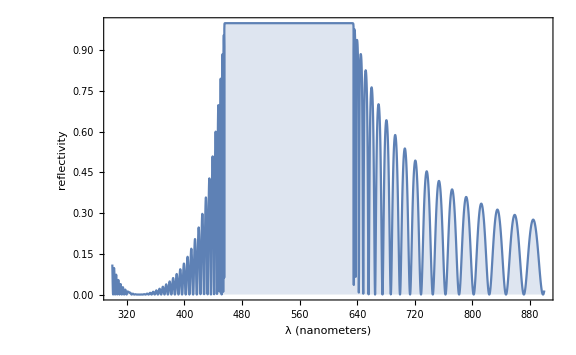

```mathematica
Plot[rE[65/(10^9 1),65/(10^9 1),1.5,2.62,50,((2 π) 3 10^8)/(λ/10^9),Pi/9],{λ,300,900},ImageSize-> Large, BaseStyle-> {FontFamily-> "Helvetica",Large},Frame-> True, FrameLabel->{"λ (nanometers)","reflectivity"},Filling-> Axis]
```

```mathematica
stackGraphic[n1_, n2_, lone_, ltwo_, numlay_,θ_]:=
Module[{r1,r2, gO},
r1 ={GrayLevel[0.99 Exp[-n1/10]],EdgeForm[Thin], Rectangle[{0,0},{lone,1600}]};
r2 ={GrayLevel[0.99 Exp[-n2/10]], EdgeForm[Thin],Rectangle[{lone,0},{(ltwo + lone),1600}]};
gO = {r1,r2};
{Table[Translate[gO,{n (lone+ ltwo),0}],{n,0, numlay-1,1}],
{Red,Line[{{-1200 Cos[Pi θ/180],800 -1200Sin[Pi θ/180]},{0,800},{-1200 Cos[Pi θ/180], 800 + 1200Sin[Pi θ/180]}}]}}
]
```

```mathematica
view[mode_,lone_,ltwo_,n1_,n2_,numlay_,tin_,lmin_,lmax_,lamloc_]:=Module[
{func},
func=If[mode==="TM",rM,rE];

Plot[func[lone/(10^9 1),ltwo/(10^9 1),n1,n2,numlay,((2 π) 3 10^8)/(λ/10^9),tin Pi/180],{λ,lmin,lmax},ImageSize-> Large, PlotRange-> {{lmin,lmax},All},AxesOrigin->{0,0},BaseStyle-> {FontFamily-> "Helvetica",18},Frame-> True, FrameLabel->{"λ (nanometers)","r^2"},
PlotLabel:>  "Reflectance Versus Wavelength "<>If[mode=="TE","TE","TM"] <>"\n n_α="<>ToString[n1]<>"  n_β="<>ToString[n2]<>"   θ_in="<>ToString[tin]<>"\n t_α="<>ToString[lone]<>"  t_β="<>ToString[ltwo]<>"  Layers= "<>ToString[numlay] ,Filling-> 0,
Epilog-> {Line[{{lamloc,0},{lamloc,1}}]}]
]
```

```mathematica
data[mode_,lone_,ltwo_,n1_,n2_,numlay_,tin_,lmin_,lmax_,nDataPoints_]:=Module[
{func},
func=If[mode==="TM",rE,rM];

Flatten@Table[func[lone/10^9,ltwo/10^9,n1,n2,numlay,((2 π) 3 10^8)/(λ/10^9),tin Pi/180],{λ,lmin,lmax,(lmax-lmin)/nDataPoints}]
]
```

#### Final Output

```mathematica
Manipulate[
Quiet@Column[{
view[mode,lone,ltwo,n1,n2,numlay,tin,lmin,lmax,lamloc],
Graphics[stackGraphic[n1,n2,4lone,4ltwo,numlay,tin],ImageSize-> Large]
}]
,
(*Style["Light Properties","Subsubsubsection"],*)
Delimiter,
{{mode,"TE","Mode"},{"TE"->"Tranverse Electic (E-parallel)","TM"-> "Transverse Magnetic (H-parallel)"},ControlType-> PopupMenu},
{{tin,25,"θ_in"},0,1
80,Appearance-> "Open",AppearanceElements-> "InputField",ContinuousAction-> False},
(*Style["Material Properties","Subsubsubsection"],*)
Delimiter,
{{n1,1.5,"Index α"},1,20,Appearance-> "Open",AppearanceElements-> "InputField",ContinuousAction-> False},
{{n2,2.62,"Index β"},1,20,Appearance-> "Open",AppearanceElements-> "InputField",ContinuousAction-> False},
{{lone,65,"Width α (nm)"},1,500,Appearance-> "Open",AppearanceElements-> "InputField",ContinuousAction-> False},
{{ltwo,65,"Width β (nm)"},1,500,Appearance-> "Open",AppearanceElements-> "InputField",ContinuousAction-> False},
{{numlay,50, "Number of Layers"}, 2,100,1,Appearance-> "Open",AppearanceElements-> "InputField",ContinuousAction-> False},
(*Style["Display Controls","Subsubsubsection"],*)
Delimiter,
{{lmin,300,"λ_min"},0,600,Appearance-> "Open",AppearanceElements-> "InputField"},
{{lmax,900,"λ_max"},lmin,1200,Appearance-> "Open",AppearanceElements-> "InputField",ContinuousAction-> False},
{{lamloc,525,"λ guide line"},lmin-100,lmax+100,Appearance-> "Open",AppearanceElements-> "InputField",ContinuousAction-> True},
(*Style["Export Controls","Subsubsubsection"],*)
Delimiter,
Button[
"Export Image",
Module[
{currentgraphic,nm},
currentgraphic=Column[{
view[mode,lone,ltwo,n1,n2,numlay,tin,lmin,lmax,lamloc],
Graphics[stackGraphic[n1,n2,4lone,4ltwo,numlay,tin],ImageSize-> Large]
}];
nm=SystemDialogInput["FileSave",{"filename_Lab_2013.tiff",{"TIFF"->{"filename.tiff"},"GIF"->{"filename.gif"},"PNG"->{"filename.png"}}}];
If[
nm=!=$Canceled,
Export[nm,currentgraphic];
];
],
Method->"Queued"
],
Button[
"Export Data",
Module[
{dataX,dataY,currentData,nm},
dataY=data[mode,lone,ltwo,n1,n2,numlay,tin,lmin,lmax,10000];
dataX=N@Range[lmin,lmax,(lmax-lmin)/10000];
currentData=Transpose@{dataX,dataY};
nm=SystemDialogInput["FileSave",{"filename_Lab_2013.csv",{"CSV"->{"filename.csv"}}}];
If[
nm=!=$Canceled,
Export[nm,currentData];
];
],
Method->"Queued"
],
LabelStyle-> Medium,SaveDefinitions-> True,Initialization:>(Off[Infinity::indet])
]
```